# Coordinatization Tutorial

Graph coordinatization means assigning labels—typically numbers—to vertices so that relations among the labels mirror relations among the corresponding vertices with respect to the underlying graph and some auxiliary structure. A naive approach is to choose a basepoint and use paths from it as labels, but such labels carry no useful structure. In practice, we use numeric coordinates that support algebra and design the coordinatization so that geometric relations become algebraic ones, allowing geometric problems to be solved numerically. This is the role of the Cartesian frame in the Euclidean plane, which turn primitive‑based Euclidean geometry into analytic and algebraic geometry. For graphs, different structures and coordinatization schemes are conceivable, and they need not be numerical. The goal of this tutorial is to explore these ideas, starting from naive implementations of familiar constructions.

#### Classical coordinatizations

This paclet implements the following numerical coordinatization schemes for graphs:

Radar coordinates — distances from selected points.

Orthogonal coordinates — shortest‑path distances from selected lines.

Rectilinear coordinates — coordinates defined via parallelism.

Radar coordinates are simple and robust, but they may collapse distant vertices or separate nearby ones.  They do not seem to preserve any geometric properties of the graph but serve merely as a mean of “triangulating” a point. Orthogonal coordinates can be used to pullback the Euclidean structure from labels to graph vertices. We can attempt to define the Euclidean structure on the graph by defining the affine structure using the notion of parallels and path-length and the inner product using the shortest path distance and the infra angle. This can be then compared with the pulled back Euclidean structure. Note that in contrast to the plane, graphs are generally anisotropic, so one expects point dependence, except possibly for some isotropic graphs. Orthogonal coordinates preserve the distances to axes by definition, which is part of the inner product. Rectilinear coordinates preserve parallelism by construction, which is part of the affine structure.

#### Note: Assigning Riemannian geometry to a graph

A mathematically straightforward approach is to consider an r-isometric embedding (preserving mutual distances of all points with distance less than r) of the graph into a Euclidean space and then apply manifold‑learning or data‑analysis methods to identify Riemannian manifolds whose discretizations could correspond to the resulting point cloud, possibly under suitable assumptions on how the points are sprinkled, and suitable assumptions on the scale. For r=1 this reduces to an embedding that preserves edge lengths (e.g. SpringEmbedding in Wolfram), while for r=diam(G) one obtains a fully isometric embedding that intertwines the graph distance to the Euclidean distance. In the former case with edge length 1, the minimal dimension such embedding may exist is given by the size of the largest clique minus 1.  In the latter case the underlying manifold must lie in an affine subspace, typically 1-dimensional, since the graph metric is geodesic and the only curves realizing Euclidean distances are straight lines. Neither the embedding nor the inferred Riemannian manifold is unique, so one naturally obtains an entire moduli space of admissible geometries. Note that the Nash embedding theorem guarantees that any Riemannian manifold can be realized as a submanifold of the Euclidean space, so we do not miss anything. Note that an optimal statement would be that sampling a sufficiently graph at a sufficiently large scale determines almost surely a unique quasi-isomorphism class of Riemannian manifolds, or in the case of hypergraph rewriting, that there is a unique Gromov-Hausdorff limit.

## Setup

```mathematica
PacletDirectoryLoad[FileNameJoin[{NotebookDirectory[], "../../.."}]];
```

```mathematica
Needs["WolframInstitute`SyntheticInfrageometry`"]
```

```mathematica
g= MeshConnectivityGraph[ DiscretizeRegion[Rectangle[], MaxCellMeasure->.02, PrecisionGoal->Infinity] ];
```

## Radar coordinates

Given a tuple of vertices, radar coordinates of another vertex is a vector of distances to these points. A spanning set is a tuple of points such that the radar coordinates are injective; that is, they distinguish every vertex. A radar basis is a minimal spanning set.

Find a radar basis of a discretization of a square:

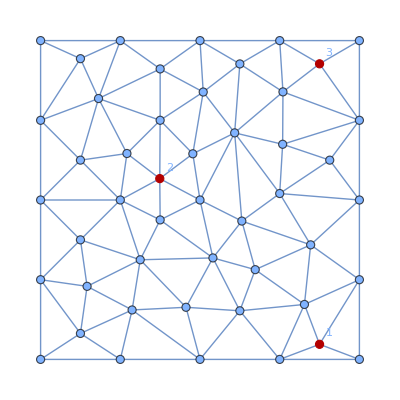

```mathematica
b = First @ FindRadarBasis[g];
HighlightGraph[g,MapIndexed[Labeled[#1,#2[[1]]]&,b]]
```

Find out how many radar bases is there among all minimal tuples:

```mathematica
bb=GroupBy[Subsets[VertexList[g],{Length @ b}],RadarBasisQ[g,#]&];
Length /@ bb
```

<|False→17284,True→12|>

Select a basis with vertices closest to each other:

```mathematica
b = First @ MinimalBy[bb[True],Total[GraphDistance[g,##]&@@@Subsets[#,{2}]]&]
```

{{0,3},{0,5},{0,43}}

Find radar coordinates and visualize their level sets (shells)

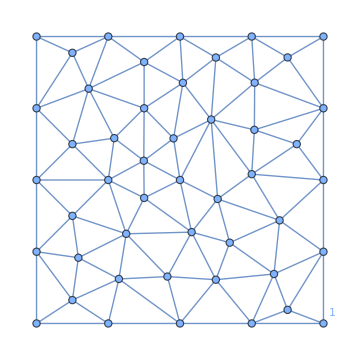
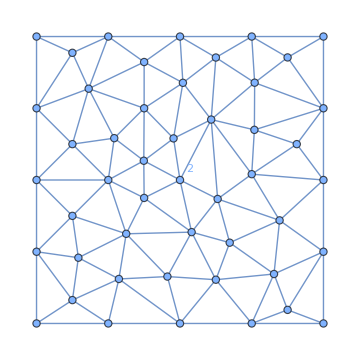
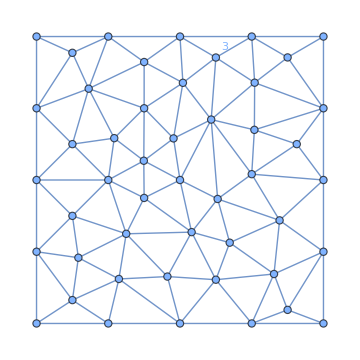

```mathematica
c = RadarCoordinates[g, b];
With[{d = Length[First[Values[c]]]},
  Row @ Table[
    With[{
      levelSets = KeySort[GroupBy[Keys[c], c[#][[i]] &]],
      maxCoordinate = Max[Values[c][[All, i]]],
      baseHue = i / (d + 1)
    },
      HighlightGraph[g,
        Append[
          KeyValueMap[
            {coordinate, vertices} |-> Style[
              Subgraph[g, vertices],
              Directive[Thick, Hue[baseHue, 0.9, 1.0 - 0.7 * coordinate / maxCoordinate]]
            ],
            levelSets
          ],
          Style[Labeled[b[[i]],i], Directive[Red, PointSize[Large]]]
        ],
        ImageSize -> Medium
      ]
    ],
    {i, d}
  ]
]
```

## Orthogonal Coordinates

Pick a small set of well-separated longest paths (or DAGs) as axes; project each vertex onto each axis and take the layer index. The result is a tuple of non-negative integers (or signed integers, when an origin is chosen). The algorithm is constructed in such a way that the orthogonal projections onto axes on the graph agree with the orthogonal projections on the axes in the pulled back Euclidean structure.

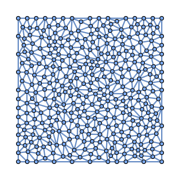
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

InfraPoint[{{0,38}}]

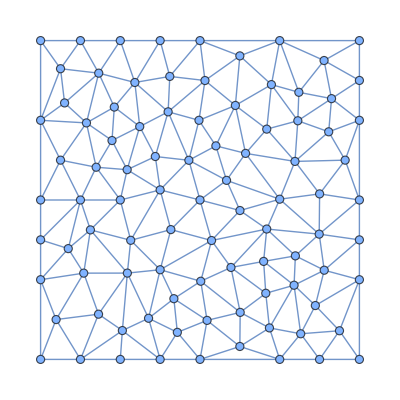

```mathematica
orthogonalFrames=Table[
With[{frame=FindOrthogonalFrame[g,c,"AxisLength"->r,"BranchSampleSize"->3,"AllowPartial"->True],bdry=Select[VertexList[g],InfraDistance[g,c,#]==r&]},<|"Radius"->r,"Frame"->frame,"Boundary"->bdry|>],{r,1,VertexEccentricity[g,c["First"]]}];

Row[frames/. data_:>With[{r=data["Radius"],frame=data["Frame"],bdry=data["Boundary"]},HighlightGraph[g,Join[Catenate@MapThread[{axis,color}|->Join[Style[#,color,PointSize[Medium]]&/@axis,Style[#,color,Thick]&/@(UndirectedEdge@@@Partition[axis,2,1])],{frame,Hue[#,0.35,0.9]&/@Subdivide[0.33,0.78,Max[Length[frame]-1,1]]}],Style[#,Red,PointSize[Medium]]&/@bdry,Style[#,Red,Thick]&/@EdgeList[Subgraph[g,bdry]],{Style[c["First"],Red,PointSize[Large]]}],ImageSize->180]]]
```

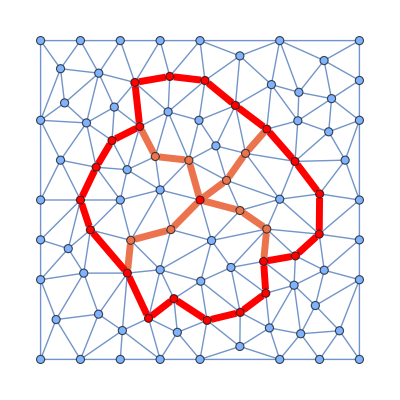

```mathematica
g= MeshConnectivityGraph[ DiscretizeRegion[Rectangle[], MaxCellMeasure->.01] ];
c=FindPoint[g,"From"->"Center"];
r=3;
f = FindOrthogonalFrame[ g, c, All,"AxisLength" -> r];
InfraSceneHighlight[g,Join[f[[1]],{c->Red, FindShell[g,c,r]->Red}]]
```

InfraShell[{{{0,1},{0,2},{0,10},{0,16},{0,18},{0,20},{0,22},{0,28},{0,31},{0,35},{0,40},{0,44},{0,46}}}]

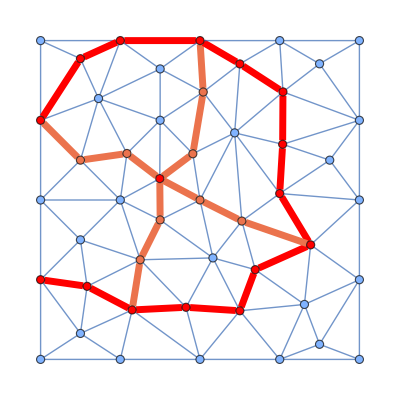

```mathematica
FindShell[g,c,4]
```